```mathematica
SetDirectory["/Users/matangrinberg/PycharmProjects/Quantum"];
```

```mathematica
n3data1=Import["N3testRange400010.03.2019.22.33.12.csv"];
n3data2=Import["N3testRange400010.03.2019.22.39.48.csv"];
n5data1=Import["N5testRange400010.07.2019.11.53.25.csv"];
n7data1=Import["N7testRange400010.07.2019.12.15.40.csv"];
average[data_]:=Total[Flatten[data]]/Length[Flatten[data]];
```

```mathematica
average[n3data2]
```

0.613051

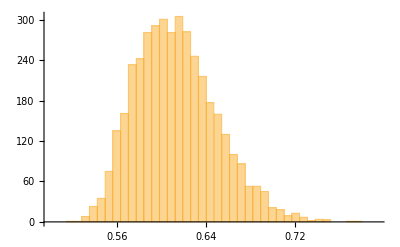

```mathematica
Histogram[n3data2,{0.5,0.8,0.007}]
```

```mathematica
average[n7data1]
average[n5data1]
average[n3data1]
```

0.624523

0.623107

0.614665

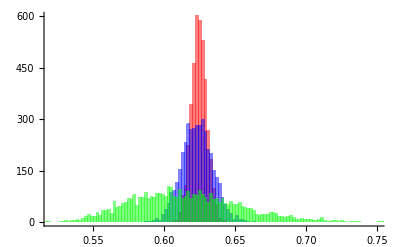

```mathematica
g1=Histogram[n7data1,{0.5,0.8,0.002},ChartStyle->{Red}];
g2=Histogram[n5data1,{0.5,0.8,0.002},ChartStyle->{Directive[Blue,Opacity[.5]]}];
g3=Histogram[n3data1,{0.5,0.8,0.002},ChartStyle->{Directive[Green,Opacity[.5]]}];
Show[g1,g2,g3,PlotRange->{{.52,.75},{0,600}}]
```

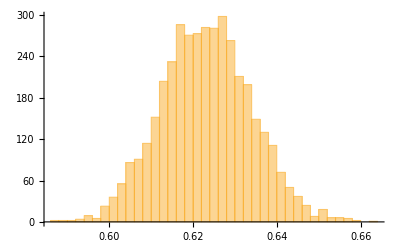

```mathematica
splt2=Histogram[n5data1,30]
```

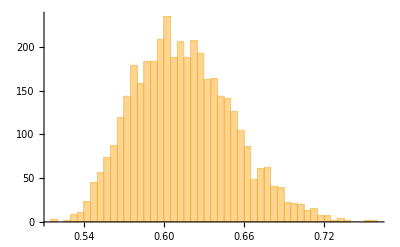

```mathematica
splt=Histogram[n3data2,35]
```

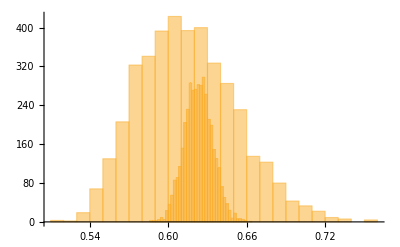

```mathematica
Show[plt2,plt5]
```

```mathematica
plt2=Histogram[n3data1,30];
plt3=Histogram[n3data2,30,AxesLabel->{"a","B"}];
```

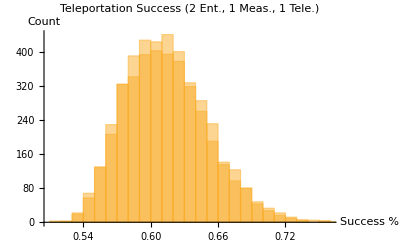

```mathematica
Show[plt2,plt3,PlotLabel->"Teleportation Success (2 Ent., 1 Meas., 1 Tele.)",AxesLabel->{"Success %","Count"}]
```

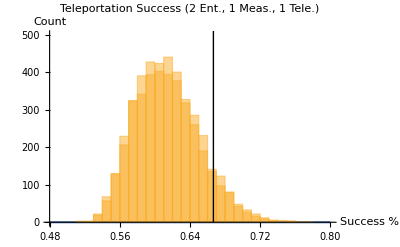

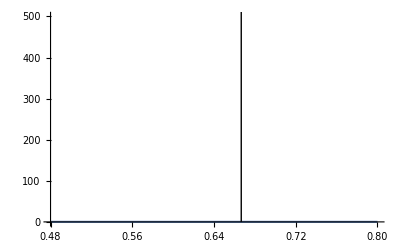

```mathematica
plt1=Plot[0,{x,.48,.8},Epilog->Line[{{2/3,0},{2/3,1000}}],PlotRange->{0,500}]
```